```mathematica
me=0.51;
mHe=2788.71;
d=20.21;
mHes=mHe+d;
fE[Ep_,Em_]:=mHes^2-mHe^2-2mHe(Ep+Em)+4Ep Em;
Epmin=me;
Epmax=(((mHes-me)^2-mHe^2+me^2)/(2(mHes-me)));
am[Ep_]:=1/(2(mHes(mHe-2Ep)+me^2));
bm[Ep_]:=(mHes-Ep)(mHes(mHes-2Ep)-mHe^2+2me^2);
cm[Ep_]:=(mHes^2-Ep^2)((mHes(mHes-2Ep)-mHe^2)^2-4mHe^2me^2);
Emmin[Ep_]:=am[Ep]*(bm[Ep]-Sqrt[cm[Ep]]);
Emmax[Ep_]:=am[Ep]*(bm[Ep]+Sqrt[cm[Ep]]);
```

```mathematica
Ep=10.40;

Epmin
Epmax
Epmin+Epmax
Print["am=",am[Ep]]
Print["bm=",bm[Ep]]
Print["Sqrt[cm]=",Sqrt[cm[Ep]]]
Print["Emmin=",Emmin[Ep]]
Print["Emmax=",Emmax[Ep]]
```

0.51

19.631

20.141

am=6.431×10^-8

bm=1.53088×10^8

Sqrt[cm]=1.53446×10^8

Emmin=-0.0230567

Emmax=19.7132

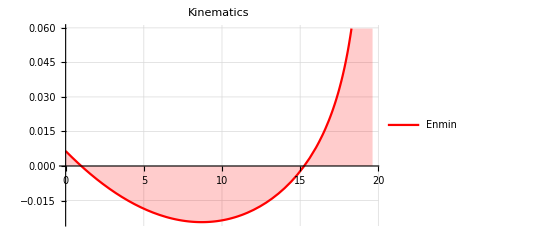

```mathematica
Plot[{Emmin[Ep]},{Ep,0Epmin,Epmax},
FrameLabel->{"Ep","Enmin"},
PlotLabel->"Kinematics",
PlotLegends->Placed[{"Enmin","Enmax"},Center],
Filling->Axis,PlotStyle->{Blue,Red},
BaseStyle->{FontSize->16},
GridLines->Automatic]
```

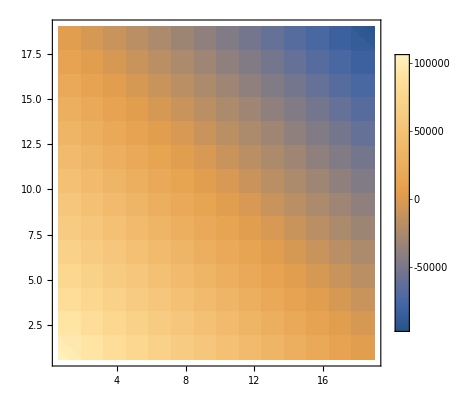

```mathematica
DensityPlot[fE[Ep,Em],{Ep,0.6,19.},{Em,0.6,19.},PlotLegends->Automatic]
```

```mathematica
q2[Ep_,Em_]:=4Ep Em;
e0[Ep_,Em_]:=Ep+Em;
dq2dEp[Ep_,Em_]:=4Em;
dq2dEm[Ep_,Em_]:=4Ep;
de0dEp[Ep_,Em_]:=1;
de0dEm[Ep_,Em_]:=1;
```

SetDelayed::write: Tag Plus in (10.4+Em)[Ep_,Em_] is Protected.

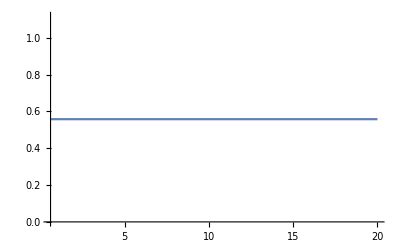

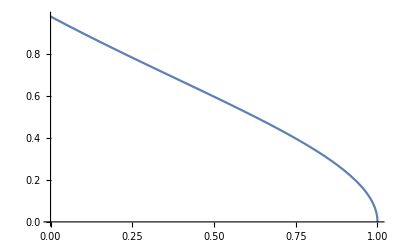

```mathematica
gx[Ex_,mx_]:=Ex/mx;
vx[Ex_,mx_]:=Sqrt[1-(mx/Ex)^2];
tp[Ex_,mx_,Cs_]:=ArcTan[  Sqrt[1-Cs^2]/(gx[Ex,mx](  Cs+vx[Ex,mx]))];
tm[Ex_,mx_,Cs_]:=ArcTan[-Sqrt[1-Cs^2]/(gx[Ex,mx](-Cs+vx[Ex,mx]))];
dt[Ex_.mx_,Cs_]:=tp[Ex,mx,Cs]-tm[Ex,mx,Cs];
Plot[vx[20.49,17],{mx,0.6,20.}]
Plot[tp[20.49,17.,Cs],{Cs,0.,1.}]
```